# ActoNet : Comparison of inference solutions and data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Franck D\Dropbox\ActONet-STOG\NoteBook-Sc-Proof\Bladder

In this notebook, we compare the patients’ molecular profiles with the solutions of inference for necessary and possible proliferation.

## Solutions and Profiles sets

Formatted solutions

```mathematica
FormattedSol={{CyclinD1->True,EGFR->True},{FGFR3,PI3K,CyclinD1->True},{PI3K,RAS,CyclinD1->True},{EGFR->True,MDM2->True,p16INK4a->False},{PI3K,EGFR->True,p16INK4a->False},{FGFR3,PI3K,p16INK4a->False},{PI3K,RAS,p16INK4a->False},{TP53,EGFR->True,p16INK4a->False},{EGFR->True,RB1->False,RBL2->False},{EGFR->True,MDM2->True,RBL2->False},{EGFR->True,p16INK4a->True,RBL2->False},{PI3K,EGFR->True,RBL2->False},{FGFR3,PI3K,RBL2->False},{PI3K,RAS,RBL2->False},{TP53,EGFR->True,RBL2->False}}
```

{{CyclinD1→True,EGFR→True},{FGFR3,PI3K,CyclinD1→True},{PI3K,RAS,CyclinD1→True},{EGFR→True,MDM2→True,p16INK4a→False},{PI3K,EGFR→True,p16INK4a→False},{FGFR3,PI3K,p16INK4a→False},{PI3K,RAS,p16INK4a→False},{TP53,EGFR→True,p16INK4a→False},{EGFR→True,RB1→False,RBL2→False},{EGFR→True,MDM2→True,RBL2→False},{EGFR→True,p16INK4a→True,RBL2→False},{PI3K,EGFR→True,RBL2→False},{FGFR3,PI3K,RBL2→False},{PI3K,RAS,RBL2→False},{TP53,EGFR→True,RBL2→False}}

Formatted Patient profile

```mathematica
ProfileSet={{CyclinD1->True,E2F3->True,p16INK4a->False},{TP53,CyclinD1->True,p16INK4a->False},{CyclinD1->True,EGFR->True,p16INK4a->False},{TP53,MDM2->False,RB1->False},{FGFR3,MDM2->True,p16INK4a->False},{RAS,MDM2->True,p16INK4a->False},{E2F3->False,p16INK4a->False,RBL2->True},{CyclinD1->True,MDM2->True,p16INK4a->False},{TP53,E2F3->True,RBL2->False},{TP53,E2F3->True,EGFR->True},{FGFR3,EGFR->False,p16INK4a->False},{TP53,RB1->False,RBL2->False},{TP53,CyclinD1->True,RB1->False},{MDM2->True,p16INK4a->False,RBL2->False},{TP53,CyclinD1->False,E2F3->True},{CyclinD1->True,p16INK4a->False,RBL2->False},{RAS,CyclinD1->True,RBL2->False},{FGFR3,p16INK4a->False,RBL2->True},{FGFR3,CyclinD1->True,p16INK4a->False},{FGFR3,p16INK4a->False,RBL2->False},{FGFR3,TP53,p16INK4a->False},{PI3K,CyclinD1->True,p16INK4a->False},{FGFR3,MDM2->True,RB1->True},{TP53,EGFR->True,p16INK4a->False},{TP53,CyclinD1->False,p16INK4a->False},{PI3K,TP53,p16INK4a->False},{CyclinD1->True,p16INK4a->False,RB1->False},{E2F3->True,MDM2->True,p16INK4a->False},{CyclinD1->True,EGFR->True,MDM2->True,p16INK4a->False},{TP53,E2F3->True,p16INK4a->False,RB1->False},{TP53,CyclinD1->True,E2F3->True,RB1->True},{FGFR3,PI3K,TP53,p16INK4a->False},{TP53,CyclinD1->True,p16INK4a->False,RB1->False},{TP53,CyclinD1->True,E2F3->True,RBL2->False},{TP53,CyclinD1->True,p16INK4a->False,RBL2->False},{RAS,CyclinD1->True,EGFR->True,p16INK4a->False},{TP53,E2F3->True,EGFR->True,RB1->False},{RAS,EGFR->True,p16INK4a->False,RB1->False},{FGFR3,E2F3->True,p16INK4a->False,RB1->False},{FGFR3,CyclinD1->True,p16INK4a->False,RBL2->False},{FGFR3,EGFR->True,p16INK4a->False,RB1->True},{RAS,E2F3->True,MDM2->True,p16INK4a->False},{CyclinD1->True,E2F3->True,MDM2->True,p16INK4a->False},{TP53,CyclinD1->True,EGFR->True,p16INK4a->False},{FGFR3,PI3K,EGFR->False,p16INK4a->False},{FGFR3,TP53,EGFR->True,p16INK4a->False},{TP53,EGFR->True,p16INK4a->False,RBL2->False},{TP53,CyclinD1->True,E2F3->True,p16INK4a->False},{FGFR3,TP53,CyclinD1->True,RBL2->False},{FGFR3,EGFR->True,MDM2->True,p16INK4a->False,RBL2->True},{CyclinD1->True,MDM2->True,p16INK4a->False,RB1->False,RBL2->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,MDM2->True},{TP53,EGFR->True,p16INK4a->False,RB1->False,RBL2->False},{TP53,CyclinD1->True,EGFR->True,MDM2->True,p16INK4a->False},{CyclinD1->True,E2F3->True,EGFR->True,MDM2->True,p16INK4a->True},{FGFR3,PI3K,CyclinD1->True,p16INK4a->False,RB1->True},{TP53,CyclinD1->True,E2F3->True,EGFR->True,RBL2->True},{FGFR3,PI3K,CyclinD1->True,E2F3->True,p16INK4a->False},{FGFR3,CyclinD1->True,EGFR->False,p16INK4a->False,RBL2->True},{CyclinD1->True,EGFR->True,p16INK4a->False,RB1->False,RBL2->False},{TP53,EGFR->True,MDM2->True,p16INK4a->False,RB1->False},{CyclinD1->True,EGFR->False,p16INK4a->False,RB1->False,RBL2->False},{TP53,CyclinD1->False,E2F3->True,EGFR->False,RBL2->False},{FGFR3,CyclinD1->True,MDM2->True,p16INK4a->False,RB1->False},{FGFR3,TP53,EGFR->True,p16INK4a->False,RB1->True},{FGFR3,TP53,CyclinD1->True,EGFR->True,p16INK4a->False},{E2F3->False,EGFR->True,p16INK4a->False,RB1->True,RBL2->True},{TP53,E2F3->False,EGFR->True,MDM2->False,p16INK4a->False},{RAS,E2F3->False,MDM2->False,p16INK4a->False,RBL2->False},{CyclinD1->False,E2F3->True,EGFR->False,MDM2->True,RBL2->False},{FGFR3,PI3K,CyclinD1->False,E2F3->False,p16INK4a->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,RB1->False,RBL2->True},{CyclinD1->True,E2F3->True,EGFR->False,MDM2->True,RB1->False,RBL2->False},{RAS,TP53,CyclinD1->True,E2F3->True,EGFR->True,MDM2->True},{CyclinD1->True,E2F3->False,MDM2->True,p16INK4a->False,RB1->False,RBL2->True},{TP53,CyclinD1->True,E2F3->True,EGFR->False,RB1->False,RBL2->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,MDM2->True,p16INK4a->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,p16INK4a->False,RB1->True},{PI3K,CyclinD1->True,E2F3->True,EGFR->False,MDM2->True,p16INK4a->False},{PI3K,TP53,CyclinD1->False,E2F3->True,RB1->False,RBL2->False},{CyclinD1->True,E2F3->True,EGFR->True,MDM2->True,p16INK4a->False,RB1->False},{TP53,CyclinD1->True,EGFR->True,MDM2->True,p16INK4a->False,RBL2->True},{TP53,E2F3->True,EGFR->True,MDM2->False,p16INK4a->False,RB1->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,p16INK4a->False,RB1->False,RBL2->False},{TP53,CyclinD1->False,E2F3->True,EGFR->True,MDM2->False,p16INK4a->True,RB1->False},{PI3K,CyclinD1->True,E2F3->True,EGFR->True,MDM2->False,RB1->True,RBL2->False},{TP53,CyclinD1->False,E2F3->False,EGFR->False,MDM2->False,RB1->False,RBL2->False},{FGFR3,CyclinD1->True,E2F3->True,EGFR->True,p16INK4a->False,RB1->True,RBL2->True},{TP53,CyclinD1->True,E2F3->True,EGFR->True,p16INK4a->True,RB1->False,RBL2->True},{FGFR3,PI3K,TP53,E2F3->True,p16INK4a->False,RB1->True,RBL2->False},{TP53,CyclinD1->True,E2F3->True,EGFR->True,MDM2->False,p16INK4a->True,RB1->False,RBL2->False}}
```

{{CyclinD1→True,E2F3→True,p16INK4a→False},{TP53,CyclinD1→True,p16INK4a→False},{CyclinD1→True,EGFR→True,p16INK4a→False},{TP53,MDM2→False,RB1→False},{FGFR3,MDM2→True,p16INK4a→False},{RAS,MDM2→True,p16INK4a→False},{E2F3→False,p16INK4a→False,RBL2→True},{CyclinD1→True,MDM2→True,p16INK4a→False},{TP53,E2F3→True,RBL2→False},{TP53,E2F3→True,EGFR→True},{FGFR3,EGFR→False,p16INK4a→False},{TP53,RB1→False,RBL2→False},{TP53,CyclinD1→True,RB1→False},{MDM2→True,p16INK4a→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True},{CyclinD1→True,p16INK4a→False,RBL2→False},{RAS,CyclinD1→True,RBL2→False},{FGFR3,p16INK4a→False,RBL2→True},{FGFR3,CyclinD1→True,p16INK4a→False},{FGFR3,p16INK4a→False,RBL2→False},{FGFR3,TP53,p16INK4a→False},{PI3K,CyclinD1→True,p16INK4a→False},{FGFR3,MDM2→True,RB1→True},{TP53,EGFR→True,p16INK4a→False},{TP53,CyclinD1→False,p16INK4a→False},{PI3K,TP53,p16INK4a→False},{CyclinD1→True,p16INK4a→False,RB1→False},{E2F3→True,MDM2→True,p16INK4a→False},{CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False},{TP53,E2F3→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,RB1→True},{FGFR3,PI3K,TP53,p16INK4a→False},{TP53,CyclinD1→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,RBL2→False},{TP53,CyclinD1→True,p16INK4a→False,RBL2→False},{RAS,CyclinD1→True,EGFR→True,p16INK4a→False},{TP53,E2F3→True,EGFR→True,RB1→False},{RAS,EGFR→True,p16INK4a→False,RB1→False},{FGFR3,E2F3→True,p16INK4a→False,RB1→False},{FGFR3,CyclinD1→True,p16INK4a→False,RBL2→False},{FGFR3,EGFR→True,p16INK4a→False,RB1→True},{RAS,E2F3→True,MDM2→True,p16INK4a→False},{CyclinD1→True,E2F3→True,MDM2→True,p16INK4a→False},{TP53,CyclinD1→True,EGFR→True,p16INK4a→False},{FGFR3,PI3K,EGFR→False,p16INK4a→False},{FGFR3,TP53,EGFR→True,p16INK4a→False},{TP53,EGFR→True,p16INK4a→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,p16INK4a→False},{FGFR3,TP53,CyclinD1→True,RBL2→False},{FGFR3,EGFR→True,MDM2→True,p16INK4a→False,RBL2→True},{CyclinD1→True,MDM2→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True},{TP53,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False},{CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→True},{FGFR3,PI3K,CyclinD1→True,p16INK4a→False,RB1→True},{TP53,CyclinD1→True,E2F3→True,EGFR→True,RBL2→True},{FGFR3,PI3K,CyclinD1→True,E2F3→True,p16INK4a→False},{FGFR3,CyclinD1→True,EGFR→False,p16INK4a→False,RBL2→True},{CyclinD1→True,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,EGFR→True,MDM2→True,p16INK4a→False,RB1→False},{CyclinD1→True,EGFR→False,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True,EGFR→False,RBL2→False},{FGFR3,CyclinD1→True,MDM2→True,p16INK4a→False,RB1→False},{FGFR3,TP53,EGFR→True,p16INK4a→False,RB1→True},{FGFR3,TP53,CyclinD1→True,EGFR→True,p16INK4a→False},{E2F3→False,EGFR→True,p16INK4a→False,RB1→True,RBL2→True},{TP53,E2F3→False,EGFR→True,MDM2→False,p16INK4a→False},{RAS,E2F3→False,MDM2→False,p16INK4a→False,RBL2→False},{CyclinD1→False,E2F3→True,EGFR→False,MDM2→True,RBL2→False},{FGFR3,PI3K,CyclinD1→False,E2F3→False,p16INK4a→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,RB1→False,RBL2→True},{CyclinD1→True,E2F3→True,EGFR→False,MDM2→True,RB1→False,RBL2→False},{RAS,TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True},{CyclinD1→True,E2F3→False,MDM2→True,p16INK4a→False,RB1→False,RBL2→True},{TP53,CyclinD1→True,E2F3→True,EGFR→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→True},{PI3K,CyclinD1→True,E2F3→True,EGFR→False,MDM2→True,p16INK4a→False},{PI3K,TP53,CyclinD1→False,E2F3→True,RB1→False,RBL2→False},{CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False,RBL2→True},{TP53,E2F3→True,EGFR→True,MDM2→False,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True,EGFR→True,MDM2→False,p16INK4a→True,RB1→False},{PI3K,CyclinD1→True,E2F3→True,EGFR→True,MDM2→False,RB1→True,RBL2→False},{TP53,CyclinD1→False,E2F3→False,EGFR→False,MDM2→False,RB1→False,RBL2→False},{FGFR3,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→True,RBL2→True},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→True,RB1→False,RBL2→True},{FGFR3,PI3K,TP53,E2F3→True,p16INK4a→False,RB1→True,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→False,p16INK4a→True,RB1→False,RBL2→False}}

```mathematica
Intersection[ProfileSet,FormattedSol]
```

{{TP53,EGFR→True,p16INK4a→False}}

## Inclusion Graph

Solutions and data are compared by the inclusion relation between data and solutions

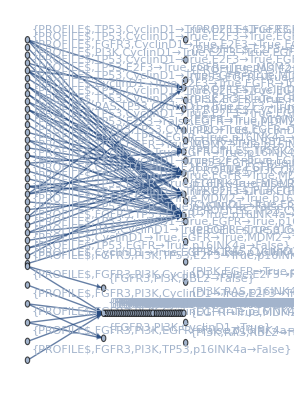

```mathematica
InclusionG=InclusionGraph[ProfileSet,FormattedSol]
```

```mathematica
Length[IncludedSolutions[InclusionG]]/Length[FormattedSol]
```

2/3

```mathematica
Length[InclusiveProfiles[InclusionG]]/Length[ProfileSet]
```

36/91

```mathematica
N[36/91]
```

0.395604

## Comparison with randomly generated solutions

We compare the precision of predictions with the precision with ranmly generated. The randomly generated solutions have the same structure (number of mutations/CNV, no incompatible perturbations ie, a->False a->True in the same set) than the inferred solution.

```mathematica
RandomInclusiveProfiles[FormattedSol,ProfileSet]
```

3/13

```mathematica
RandomIncludedSolutions[FormattedSol,ProfileSet]
```

7/15

```mathematica
TabRandomIP=Table[RandomInclusiveProfiles[FormattedSol,ProfileSet],500]
```

{3/13,10/91,18/91,25/91,20/91,40/91,8/91,12/91,27/91,19/91,20/91,2/7,12/91,20/91,10/91,2/13,30/91,1/7,19/91,33/91,3/13,15/91,19/91,9/91,29/91,2/13,5/91,2/7,18/91,9/91,1/13,20/91,20/91,10/91,16/91,1/13,8/91,12/91,25/91,31/91,12/91,15/91,15/91,3/13,20/91,11/91,16/91,2/13,2/13,12/91,2/13,1/7,12/91,9/91,4/91,23/91,23/91,27/91,40/91,12/91,1/7,16/91,17/91,1/13,27/91,11/91,18/91,1/13,2/13,8/91,11/91,9/91,10/91,12/91,1/7,2/13,16/91,12/91,10/91,33/91,1/13,19/91,17/91,22/91,24/91,19/91,3/13,22/91,1/7,11/91,16/91,6/91,23/91,17/91,8/91,23/91,8/91,9/91,16/91,15/91,12/91,36/91,17/91,3/13,8/91,23/91,8/91,3/91,15/91,2/7,11/91,10/91,23/91,15/91,8/91,17/91,23/91,41/91,10/91,34/91,41/91,10/91,1/7,10/91,18/91,3/13,1/13,8/91,20/91,9/91,15/91,17/91,10/91,31/91,4/91,18/91,5/13,1/7,3/13,22/91,23/91,9/91,15/91,24/91,29/91,1/7,30/91,12/91,12/91,17/91,3/13,11/91,4/13,11/91,15/91,10/91,19/91,16/91,9/91,43/91,11/91,16/91,3/13,9/91,8/91,11/91,16/91,16/91,29/91,20/91,9/91,1/13,25/91,19/91,12/91,36/91,15/91,22/91,12/91,11/91,12/91,9/91,6/91,5/91,15/91,12/91,18/91,3/91,1/7,17/91,16/91,9/91,11/91,32/91,23/91,12/91,1/7,18/91,46/91,1/13,23/91,2/13,11/91,19/91,19/91,23/91,22/91,19/91,24/91,2/13,1/7,10/91,18/91,25/91,9/91,12/91,24/91,12/91,20/91,2/13,27/91,3/13,17/91,4/13,23/91,30/91,4/13,2/13,24/91,17/91,23/91,24/91,17/91,10/91,16/91,38/91,1/13,22/91,10/91,3/13,18/91,12/91,23/91,5/91,18/91,1/7,9/91,18/91,34/91,19/91,20/91,20/91,10/91,3/13,23/91,2/13,1/7,12/91,25/91,12/91,10/91,17/91,12/91,2/13,2/13,20/91,24/91,11/91,3/13,16/91,15/91,3/13,15/91,15/91,19/91,5/91,22/91,27/91,22/91,18/91,16/91,4/91,17/91,24/91,17/91,15/91,6/91,2/7,12/91,17/91,17/91,18/91,3/13,3/13,18/91,10/91,17/91,5/13,10/91,15/91,9/91,9/91,25/91,1/7,18/91,2/13,16/91,20/91,10/91,3/91,11/91,1/7,19/91,23/91,16/91,46/91,22/91,5/91,15/91,1/7,10/91,12/91,15/91,18/91,11/91,8/91,1/7,10/91,15/91,1/13,23/91,8/91,20/91,12/91,4/91,18/91,17/91,20/91,8/91,6/91,17/91,19/91,9/91,22/91,2/13,16/91,25/91,12/91,12/91,34/91,1/7,12/91,2/13,19/91,8/91,23/91,12/91,2/7,30/91,24/91,18/91,9/91,9/91,15/91,2/13,2/13,11/91,25/91,18/91,5/91,17/91,15/91,19/91,25/91,20/91,1/7,4/13,9/91,11/91,8/91,18/91,18/91,11/91,15/91,8/91,24/91,15/91,3/13,6/91,15/91,11/91,18/91,5/91,15/91,10/91,1/7,16/91,12/91,1/13,2/7,16/91,24/91,34/91,1/7,8/91,4/13,12/91,11/91,2/13,3/13,11/91,4/13,23/91,1/7,3/13,19/91,18/91,2/7,20/91,22/91,27/91,43/91,10/91,19/91,1/7,1/7,18/91,25/91,23/91,3/13,11/91,3/13,1/13,16/91,11/91,20/91,1/7,29/91,11/91,2/13,20/91,8/91,19/91,8/91,2/13,3/13,1/13,36/91,5/91,2/13,3/13,11/91,23/91,4/91,15/91,10/91,16/91,2/13,15/91,22/91,1/7,1/7,17/91,12/91,10/91,17/91,2/13,1/13,3/13,6/91,25/91,18/91,22/91,2/13,2/13,17/91,19/91,2/13,10/91,22/91,10/91,2/13,19/91,27/91,8/91,24/91,19/91,12/91,11/91,11/91,22/91,15/91,8/91,41/91,16/91,22/91,12/91,12/91,1/13,10/91}

```mathematica
Mean[TabRandomIP]
```

1661/9100

```mathematica
N[2069/11375]
```

0.18189

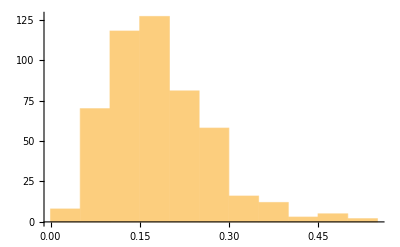

```mathematica
Histogram[TabRandomIP]
```

```mathematica
TabRandomIS=Table[RandomIncludedSolutions[FormattedSol,ProfileSet],500]
```

{4/15,2/5,7/15,4/15,1/5,7/15,2/5,8/15,8/15,8/15,1/3,8/15,11/15,4/15,7/15,2/5,3/5,7/15,8/15,3/5,7/15,2/5,11/15,8/15,7/15,7/15,7/15,2/5,2/5,1/3,7/15,3/5,1/3,7/15,8/15,4/15,2/5,1/3,1/3,11/15,8/15,7/15,7/15,1/3,8/15,3/5,4/15,2/5,2/5,2/5,1/15,1/3,3/5,11/15,7/15,8/15,2/5,4/15,2/5,7/15,8/15,4/15,8/15,8/15,1/5,4/15,2/5,8/15,7/15,8/15,7/15,2/5,7/15,1/3,1/3,2/5,8/15,7/15,2/5,1/3,7/15,1/3,8/15,4/15,7/15,2/5,1/3,8/15,4/15,2/5,7/15,1/5,3/5,3/5,3/5,1/3,8/15,1/3,1/3,1/3,2/5,1/3,7/15,8/15,2/5,2/5,8/15,4/15,7/15,1/3,11/15,8/15,2/5,2/5,1/3,2/5,3/5,2/5,2/5,7/15,4/15,1/5,2/5,2/5,2/5,7/15,7/15,2/5,4/15,3/5,1/3,8/15,2/5,2/5,8/15,3/5,7/15,8/15,4/15,1/5,3/5,3/5,2/5,2/15,1/3,7/15,8/15,8/15,7/15,2/5,4/15,8/15,2/5,7/15,1/5,4/15,1/5,7/15,11/15,4/15,7/15,8/15,8/15,1/3,7/15,8/15,1/5,2/5,8/15,8/15,1/3,2/5,7/15,7/15,8/15,2/5,8/15,3/5,8/15,3/5,11/15,4/15,1/3,3/5,7/15,2/5,7/15,7/15,8/15,8/15,1/3,8/15,8/15,1/3,2/5,4/15,7/15,4/15,3/5,7/15,2/5,2/5,2/3,2/5,8/15,2/5,8/15,2/5,2/5,1/3,1/3,3/5,2/5,8/15,8/15,2/5,7/15,2/5,1/5,7/15,3/5,2/5,1/3,3/5,1/3,1/3,1/3,8/15,2/5,1/3,8/15,2/5,1/3,7/15,4/15,3/5,2/5,7/15,2/5,7/15,7/15,7/15,8/15,4/15,1/3,7/15,1/3,7/15,1/3,3/5,7/15,2/5,7/15,2/3,1/5,1/3,2/5,2/5,7/15,2/3,2/5,1/3,3/5,2/5,2/15,4/15,4/15,1/3,3/5,1/3,2/3,2/5,7/15,4/15,1/3,1/3,7/15,2/5,1/5,3/5,8/15,4/15,4/15,7/15,8/15,2/5,8/15,7/15,1/3,1/3,2/5,4/15,3/5,7/15,1/3,1/3,3/5,7/15,3/5,1/5,7/15,2/5,8/15,8/15,4/15,8/15,7/15,8/15,2/5,2/5,2/5,7/15,3/5,2/5,1/5,7/15,7/15,2/5,2/5,2/5,1/3,8/15,3/5,8/15,1/3,7/15,7/15,7/15,2/5,7/15,3/5,2/5,7/15,8/15,2/5,4/15,8/15,8/15,7/15,8/15,7/15,8/15,2/5,8/15,7/15,2/5,1/3,2/5,3/5,7/15,1/3,7/15,3/5,7/15,1/3,8/15,1/3,1/3,1/5,1/3,7/15,1/3,8/15,2/5,1/5,2/5,1/3,4/15,1/3,1/3,7/15,8/15,7/15,7/15,7/15,7/15,1/3,1/3,1/5,2/5,8/15,2/5,8/15,3/5,7/15,7/15,8/15,2/5,4/15,4/15,4/5,8/15,7/15,8/15,2/5,2/5,4/15,4/15,1/3,1/3,1/5,2/5,3/5,11/15,4/15,2/5,2/5,7/15,2/5,8/15,2/5,2/5,8/15,7/15,1/3,1/3,2/5,2/5,8/15,4/15,3/5,8/15,2/5,2/3,3/5,1/3,7/15,1/3,7/15,8/15,7/15,8/15,1/3,7/15,8/15,8/15,1/3,7/15,7/15,8/15,2/5,8/15,3/5,8/15,2/5,7/15,2/5,1/5,4/15,7/15,1/3,1/3,8/15,2/5,1/3,7/15,2/5,7/15,2/5,2/5,1/3,1/3,1/3,8/15,1/3,7/15,8/15,2/5,7/15,11/15,1/3,2/5,2/5,7/15,4/15,2/5,2/5,4/15,8/15,2/5,1/3,3/5,7/15,4/15,3/5,4/15,8/15,8/15,1/3,8/15,4/15,2/3,8/15,7/15,7/15,11/15,2/5,3/5,1/3,4/15}

```mathematica
Mean[TabRandomIS]
```

3247/7500

```mathematica
N[1073/2500]
```

0.4292

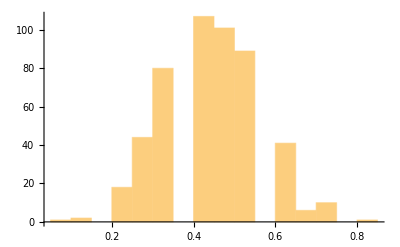

```mathematica
Histogram[TabRandomIS]
```

```mathematica
PairedTTest[TabRandomIS,Length[IncludedSolutions[InclusionG]]/Length[SolutionSet]]
```

Power::infy: Infinite expression 1/0 encountered.

PairedTTest::nllval: The argument ComplexInfinity should be an integer, a real number, or a list of such numbers with length equal to the dimensionality of the data.

PairedTTest[{4/15,2/5,7/15,4/15,1/5,7/15,2/5,8/15,8/15,8/15,1/3,8/15,11/15,4/15,7/15,2/5,3/5,7/15,8/15,3/5,7/15,2/5,11/15,8/15,7/15,7/15,7/15,2/5,2/5,1/3,7/15,3/5,1/3,7/15,8/15,4/15,2/5,1/3,1/3,11/15,8/15,7/15,7/15,1/3,8/15,3/5,4/15,2/5,2/5,2/5,1/15,1/3,3/5,11/15,7/15,8/15,2/5,4/15,2/5,7/15,8/15,4/15,8/15,8/15,1/5,4/15,2/5,8/15,7/15,8/15,7/15,2/5,7/15,1/3,1/3,2/5,8/15,7/15,2/5,1/3,7/15,1/3,8/15,4/15,7/15,2/5,1/3,8/15,4/15,2/5,7/15,1/5,3/5,3/5,3/5,1/3,8/15,1/3,1/3,1/3,2/5,1/3,7/15,8/15,2/5,2/5,8/15,4/15,7/15,1/3,11/15,8/15,2/5,2/5,1/3,2/5,3/5,2/5,2/5,7/15,4/15,1/5,2/5,2/5,2/5,7/15,7/15,2/5,4/15,3/5,1/3,8/15,2/5,2/5,8/15,3/5,7/15,8/15,4/15,1/5,3/5,3/5,2/5,2/15,1/3,7/15,8/15,8/15,7/15,2/5,4/15,8/15,2/5,7/15,1/5,4/15,1/5,7/15,11/15,4/15,7/15,8/15,8/15,1/3,7/15,8/15,1/5,2/5,8/15,8/15,1/3,2/5,7/15,7/15,8/15,2/5,8/15,3/5,8/15,3/5,11/15,4/15,1/3,3/5,7/15,2/5,7/15,7/15,8/15,8/15,1/3,8/15,8/15,1/3,2/5,4/15,7/15,4/15,3/5,7/15,2/5,2/5,2/3,2/5,8/15,2/5,8/15,2/5,2/5,1/3,1/3,3/5,2/5,8/15,8/15,2/5,7/15,2/5,1/5,7/15,3/5,2/5,1/3,3/5,1/3,1/3,1/3,8/15,2/5,1/3,8/15,2/5,1/3,7/15,4/15,3/5,2/5,7/15,2/5,7/15,7/15,7/15,8/15,4/15,1/3,7/15,1/3,7/15,1/3,3/5,7/15,2/5,7/15,2/3,1/5,1/3,2/5,2/5,7/15,2/3,2/5,1/3,3/5,2/5,2/15,4/15,4/15,1/3,3/5,1/3,2/3,2/5,7/15,4/15,1/3,1/3,7/15,2/5,1/5,3/5,8/15,4/15,4/15,7/15,8/15,2/5,8/15,7/15,1/3,1/3,2/5,4/15,3/5,7/15,1/3,1/3,3/5,7/15,3/5,1/5,7/15,2/5,8/15,8/15,4/15,8/15,7/15,8/15,2/5,2/5,2/5,7/15,3/5,2/5,1/5,7/15,7/15,2/5,2/5,2/5,1/3,8/15,3/5,8/15,1/3,7/15,7/15,7/15,2/5,7/15,3/5,2/5,7/15,8/15,2/5,4/15,8/15,8/15,7/15,8/15,7/15,8/15,2/5,8/15,7/15,2/5,1/3,2/5,3/5,7/15,1/3,7/15,3/5,7/15,1/3,8/15,1/3,1/3,1/5,1/3,7/15,1/3,8/15,2/5,1/5,2/5,1/3,4/15,1/3,1/3,7/15,8/15,7/15,7/15,7/15,7/15,1/3,1/3,1/5,2/5,8/15,2/5,8/15,3/5,7/15,7/15,8/15,2/5,4/15,4/15,4/5,8/15,7/15,8/15,2/5,2/5,4/15,4/15,1/3,1/3,1/5,2/5,3/5,11/15,4/15,2/5,2/5,7/15,2/5,8/15,2/5,2/5,8/15,7/15,1/3,1/3,2/5,2/5,8/15,4/15,3/5,8/15,2/5,2/3,3/5,1/3,7/15,1/3,7/15,8/15,7/15,8/15,1/3,7/15,8/15,8/15,1/3,7/15,7/15,8/15,2/5,8/15,3/5,8/15,2/5,7/15,2/5,1/5,4/15,7/15,1/3,1/3,8/15,2/5,1/3,7/15,2/5,7/15,2/5,2/5,1/3,1/3,1/3,8/15,1/3,7/15,8/15,2/5,7/15,11/15,1/3,2/5,2/5,7/15,4/15,2/5,2/5,4/15,8/15,2/5,1/3,3/5,7/15,4/15,3/5,4/15,8/15,8/15,1/3,8/15,4/15,2/3,8/15,7/15,7/15,11/15,2/5,3/5,1/3,4/15},ComplexInfinity]

## Patient Profile analysis

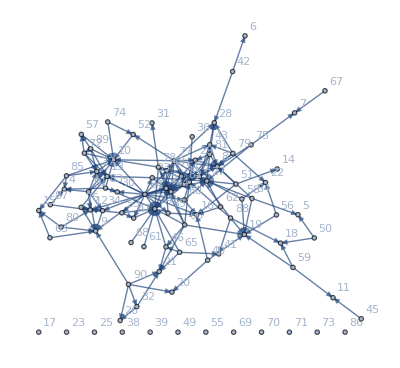

```mathematica
k=0;stratification =RelationGraph[(SubsetQ[#1,#2]&& #1 =!= #2)&,ProfileSet, VertexLabels->Function[v, v-> Tooltip[++k,v]]/@ProfileSet, ImageSize->Full,EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.009]]
```